# Kb-sample “pure fatigue” evaluation code

## Data import

## Clarify file content

```mathematica
FatigueData=ImportString[StringReplace[Import[NotebookDirectory[]<>"RawData.csv","Text"],
{","->".",";"->","}]];(*Depending on what your file looks like you might want need to use StringReplace*)
TableForm[%[[2;;5]],TableHeadings->{None,%[[1]]}]
```

## Calibration curve data

```mathematica
b=5.992; (*Calibration curve data*)
d=5.904; (*Calibration curve data*)
```

## Functions

```mathematica
AveragePotential[PotentialMax_,PotentialMin_]:=(PotentialMax+PotentialMin)/2;
PotentialDropOverCrack[averagePotential_,potentialDropStartValue_]:=averagePotential-potentialDropStartValue;
CrackArea[potentialDropOverCrack_,b_,d_]:=b*potentialDropOverCrack+d*potentialDropOverCrack^2; (* Add reference if possible *)
TotalCrackArea[crackArea_,an_,cn_]:=crackArea+π/2*an*cn; (* Crack area + notch area *)
CrackLength[totalCrackArea_]:=√((2*totalCrackArea)/π);
```

## Constants

### Check that data looks ok

```mathematica
TableForm[Select[FatigueData[[2;;]],#[[3]]==8&][[;;10]],TableHeadings->{None, FatigueData[[1]]}]
```

### Constants

```mathematica
ConstantsFilePath=NotebookDirectory[] <>"Constants.xls";
```

```mathematica
T=Import[ConstantsFilePath][[1,4,2]](*Specimen thickness [mm]*)
```

```mathematica
W=Import[ConstantsFilePath][[1,5,2]] (*Specimen width [mm]*)
```

```mathematica
an=Import[ConstantsFilePath][[1,42,2]](*Notch dimension*)
```

```mathematica
cn=Import[ConstantsFilePath][[1,43,2]] (*Notch dimension*)
```

```mathematica
averagePotentialPreCrack=Import[Test71802FilePath][[1,12,1]]  (*the average of PDs of pre-crack measurement [V]*)
PD0pre=averagePotentialPreCrack;
```

```mathematica
step=10; (* Step in between point *)
```

## Calculations

```mathematica
startTime=Select[FatigueData,#[[3]]==8&][[1,4]];(*Read in the the values you need i.e., start value an so forth*)
FatigueDataBlock8=Select[FatigueData,#[[3]]==8&];
{#[[2]]-%[[1,2]],AveragePotential[#[[10]],#[[11]]]}&/@%[[;;;;10]];
{#[[1]],PotentialDropOverCrack[#[[2]],PD0pre]}&/@%;
{#[[1]],CrackArea[#[[2]],b,d]}&/@%;
{#[[1]],TotalCrackArea[#[[2]],an,cn]}&/@%;
{#[[1]],CrackLength[#[[2]]]}&/@%;
cycleVsCrack=%;
ListPlot[cycleVsCrack,PlotLabel->Style["Fatigue, Temp, MPa", FontSize->12],PlotLegends->{"Fatigue, Temp, MPa"},AxesLabel->{"Cycle (N)" ,"Crack length a (mm)"}]
```

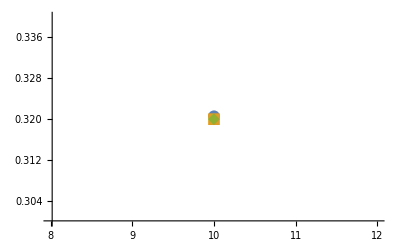

```mathematica
roundedCycleVsCrack={#[[1]],Round[#[[2]],0.01]}&/@cycleVsCrack;(*rounding data*)
roundedMeanCyclePerCrackLength ={#[[1,1]],Mean[#[[;;,2]]]}&/@Gather[roundedCycleVsCrack[[;;;;1]],#1[[1]]==#2[[1]]&];
ListPlot[{
cycleVsCrack,
roundedCycleVsCrack,
roundedMeanCyclePerCrackLength}, 
PlotRange->{{8,12},{0.3,0.34}},
PlotMarkers->{Automatic,12}]
```

```mathematica
M[a_]:=1.04+0.202*(a/T)^2-0.106*(a/T)^4;
DeltaK[a_]:=dS*√(π*a/1000)*M[a]/1.57/1000000;
```

```mathematica
crackLengthPerCycleInterpolationSimple=LinearModelFit[{#[[1]],#[[2]]}&/@roundedMeanCyclePerCrackLength[[;;;;1]],{1,x,x^2,x^3,x^4,x^5},x]
Show[{
ListPlot[roundedMeanCyclePerCrackLength[[;;;;30]],AxesLabel->{"Cycle (N)", "a"},PlotMarkers->{Automatic,10}],
Plot[crackLengthPerCycleInterpolationSimple[x],{x,0,16000},PlotStyle->Red]
}]
```

```mathematica
NadadN=Table[{x,crackLengthPerCycleInterpolationSimple[x],crackLengthPerCycleInterpolationSimple'[x]},{x,0,16000,30}];
```

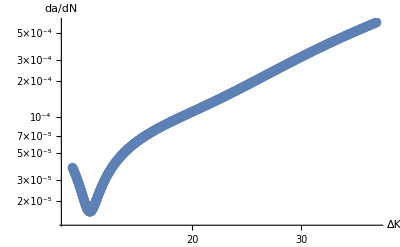

```mathematica
ListLogLogPlot[{DeltaK[#[[2]]],#[[3]]}&/@NadadN,PlotMarkers->{Automatic,10},AxesLabel->{"ΔK","da/dN"}]
Export[NotebookDirectory[]<>"FatigueDaDNDeltaK.pdf",%]
Export[NotebookDirectory[]<>"FatigueDaDNDeltaK.xlsx",{DeltaK[#[[2]]],#[[3]]}&/@NadadN]
```

```mathematica
cycleTime=2;
```

```mathematica
crackLengthPerTimeInterpolationSimple=LinearModelFit[{#[[1]]*cycleTime,#[[2]]}&/@roundedMeanCyclePerCrackLength[[;;;;1]],{1,x,x^2,x^3,x^4,x^5},x]
Plot[crackLengthPerTimeInterpolationSimple[x],{x,0,1600*cycleTime}]
```

```mathematica
tadadN=Table[{x,crackLengthPerTimeInterpolationSimple[x],crackLengthPerTimeInterpolationSimple'[x]},{x,0,16000*cycleTime,30*cycleTime}];
```

```mathematica
ListLogLogPlot[{DeltaK[#[[2]]],#[[3]]}&/@tadadN,PlotMarkers->{Automatic,10},AxesLabel->{"ΔK","da/dt"}]
Export[NotebookDirectory[]<>"FatigueDaDtKmax.pdf",%]
Export[NotebookDirectory[]<>"FatigueDaDtKmax.xlsx",{DeltaK[#[[2]]],#[[3]]}&/@tadadN]
```